# Bessel function

BesselJ[n,z] gives the Bessel function of the first kind J_n(z). 


BesselY[n,z] gives the Bessel function of the second kind Y_n(z) ... The Neumann function

It satisfies the differential equationz^2 y''+z y'+(z^2-n^2)y=0that we obtained for example in the solution of the Laplace equation in cilindrical coordenates.

       Remenber that:

n=ν is a number (It could be complex number)
       y=y(x) where x is the independent variable

#### Solution

This equation could be solve directly using Mathematica. It gives the geeral solution

```mathematica
DSolve[ x^2*y''[x] +x*y'[x]+(x^2-n^2)*y[x]==0, y[x],x]
```

{{y[x]→BesselJ[n,x] C[1]+BesselY[n,x] C[2]}}

#### Examples :

```mathematica
BesselJ[0,5.2]
BesselY[0,5.2]
```

-0.11029

-0.331251

#### Plot the Bessel J_n

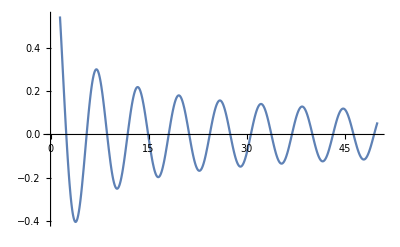

```mathematica
Plot[BesselJ[0,x],{x,0,50}]
```

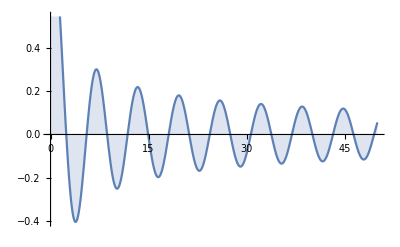

```mathematica
Plot[BesselJ[0,x],{x,0,50},Filling->Axis]
```

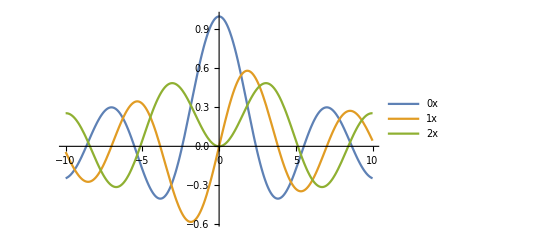

```mathematica
Plot[{BesselJ[0,x],BesselJ[1,x],BesselJ[2,x]},{x,-10,10},PlotLegends->"Expressions"]
```

#### Plot the Bessel Y_n (The Newmann solution)

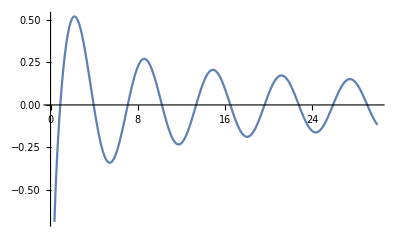

```mathematica
Plot[BesselY[0,x],{x,0,30}]
```

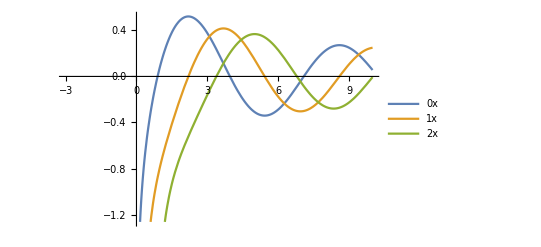

```mathematica
Plot[{BesselY[0,x],BesselY[1,x],BesselY[2,x]},{x,-3,10},PlotLegends->"Expressions"]
```

#### Series

```mathematica
Series[BesselJ[0,x],{x,0,10}]
```

1-x^2/4+x^4/64-x^6/2304+x^8/147456-x^10/14745600+O[x]^11

#### For half - integer indices, BesselJ and BesselY evaluates to elementary functions :

```mathematica
BesselJ[1/2,x]
BesselY[1/2,x]
```

(√(2/π) Sin[x])/(√x)

-(√(2/π) Cos[x])/(√x)

#### Traditional form

```mathematica
BesselJ[n,r]//TraditionalForm
BesselY[n,r]//TraditionalForm
```

nr

nr

#### Applications: The Fraunhofer diffraction